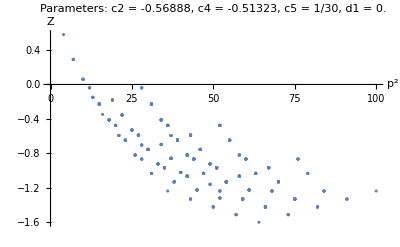

```mathematica
c2 = -.56888; 
c4 = -.51323; 
c5 = 1/30; 
d1 = 0;
L = 16;
Z[μ_] := 1;
Zhyp[ρ_] := Z[ρ . ρ] + c2 * (ρ . ρ) + c4 * (ρ[[1]]^4 + ρ[[2]]^4 + ρ[[3]]^4 + ρ[[4]]^4) / (ρ . ρ) + c5 * (ρ . ρ) * Log[ρ . ρ] + d1 / (ρ . ρ);
ptwid[p1_, p2_, p3_, p4_] := {Sin[2*Pi * p1 / L], Sin[2*Pi*p2 / L], Sin[2*Pi*p3/L], Sin[2*Pi*p4/L]};
Ztable = Table[{i^2 + j^2 + k^2 + l^2, Zhyp[ptwid[i, j, k, l]]},
 {i, 1, 5}, {j, 1, 5}, {k, 1, 5}, {l, 1, 5}];
Zlist = Flatten[Ztable, 3];
ListPlot[Zlist, AxesLabel->{p^2, Z}, PlotLabel->StringForm["Parameters: c2 = ``, c4 = ``, c5 = ``, d1 = ``. ",  c2, c4, c5, d1]]
```

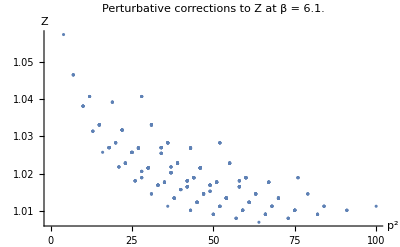

```mathematica
β = 6.1;
g = Sqrt[6 / β];
S[ρ_, n_] := ρ[[1]]^n + ρ[[2]]^n + ρ[[3]]^n + ρ[[4]]^n;
Zvb[ρ_] := 1 + g^2 * (4/3) / (16*Pi^2)*(
5.78101 - 8/3 * Log[S[ρ, 2]] + 4/9 * S[ρ, 4] / (S[ρ, 2]^2) + S[ρ, 2] * (-.56888 + 1/30 * Log[S[ρ, 2]]) + S[ρ, 4] / S[ρ, 2] * (-.51323 + 19/30 * Log[S[ρ, 2]]) + 71 / 270 * S[ρ, 4]^2 / (S[ρ, 2]^3) + 164/135*S[ρ, 6] / (S[ρ, 2]^2)
);

Zvbtable = Table[{i^2 + j^2 + k^2 + l^2, Zvb[ptwid[i, j, k, l]]},
 {i, 1, 5}, {j, 1, 5}, {k, 1, 5}, {l, 1, 5}];
Zvblist = Flatten[Zvbtable, 3];
ListPlot[Zvblist, AxesLabel->{p^2, Z}, PlotLabel->StringForm["Perturbative corrections to Z at β = ``. ", β]]
```